```mathematica
BaseCoeff[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

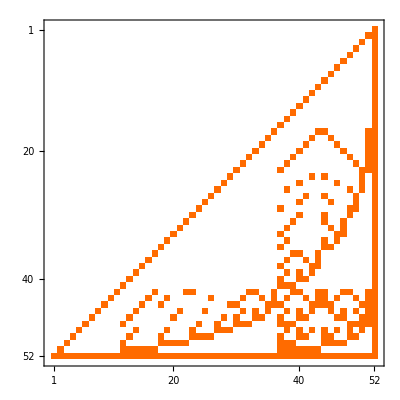

```mathematica
ConversionMatrix["E","C"]//Sort//MatrixPlot
```

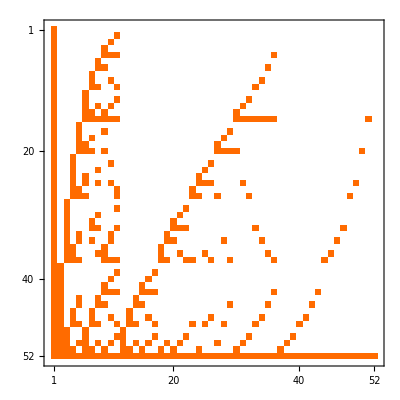

```mathematica
ConversionMatrix["G","C"]//Sort//MatrixPlot
```

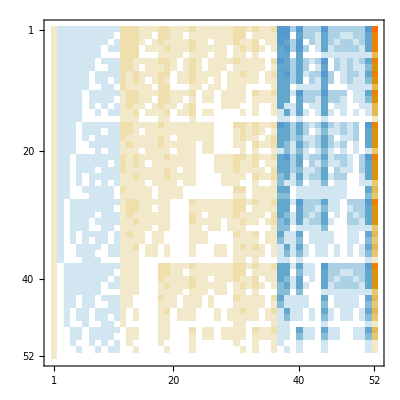

```mathematica
ConversionMatrix["G","E"]//Sort//MatrixPlot
```

```mathematica
BaseCoeff[9841,"C"]
```

{1,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
Bases["E"]
```

<|Colofour→colofourrealnull,AtomKeys→{0,39366,13122,4374,1458,486,162,54,18,6,2,52974,43902,40878,39384,39372,39368,17514,14586,13284,13176,13124,5834,4860,4428,4380,1944,1620,1476,666,546,488,218,168,72,26,57528,54492,52976,45416,43908,40896,39392,18980,17568,14748,13340,6320,4920,2124,728,59048},Variables→{n1x2x3x4x5,n12x3x4x5,n13x2x4x5,n14x2x3x5,n15x2x3x4,n1x23x4x5,n1x24x3x5,n1x25x3x4,n1x2x34x5,n1x2x35x4,n1x2x3x45,n123x4x5,n124x3x5,n125x3x4,n12x34x5,n12x35x4,n12x3x45,n134x2x5,n135x2x4,n13x24x5,n13x25x4,n13x2x45,n145x2x3,n14x23x5,n14x25x3,n14x2x35,n15x23x4,n15x24x3,n15x2x34,n1x234x5,n1x235x4,n1x23x45,n1x245x3,n1x24x35,n1x25x34,n1x2x345,n1234x5,n1235x4,n123x45,n1245x3,n124x35,n125x34,n12x345,n1345x2,n134x25,n135x24,n13x245,n145x23,n14x235,n15x234,n1x2345,n12345}|>

```mathematica
Bases["C"]
```

<|Colofour→colofour,AtomKeys→{29524,49207,36085,31711,30253,29767,29605,29551,29533,29527,29525,56011,51475,49963,49216,49210,49208,38281,36817,36166,36112,36086,32441,31954,31738,31714,30496,30334,30262,29857,29797,29768,29633,29608,29560,29537,58288,56770,56012,52232,51478,49972,49220,39014,38308,36898,36194,32684,31984,30586,29888,59048},Variables→{v1x2x3x4x5,v12x3x4x5,v13x2x4x5,v14x2x3x5,v15x2x3x4,v1x23x4x5,v1x24x3x5,v1x25x3x4,v1x2x34x5,v1x2x35x4,v1x2x3x45,v123x4x5,v124x3x5,v125x3x4,v12x34x5,v12x35x4,v12x3x45,v134x2x5,v135x2x4,v13x24x5,v13x25x4,v13x2x45,v145x2x3,v14x23x5,v14x25x3,v14x2x35,v15x23x4,v15x24x3,v15x2x34,v1x234x5,v1x235x4,v1x23x45,v1x245x3,v1x24x35,v1x25x34,v1x2x345,v1234x5,v1235x4,v123x45,v1245x3,v124x35,v125x34,v12x345,v1345x2,v134x25,v135x24,v13x245,v145x23,v14x235,v15x234,v1x2345,v12345}|>

```mathematica
Bases["G"]
```

<|Colofour→colofourgenerator,AtomKeys→{29524,9841,22963,27337,28795,29281,29443,29497,29515,29521,29523,3037,7573,9085,9832,9838,9840,20767,22231,22882,22936,22962,26607,27094,27310,27334,28552,28714,28786,29191,29251,29280,29415,29440,29488,29511,760,2278,3036,6816,7570,9076,9828,20034,20740,22150,22854,26364,27064,28462,29160,0},Variables→{g1x2x3x4x5,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g1x2x34x5,g1x2x35x4,g1x2x3x45,g123x4x5,g124x3x5,g125x3x4,g12x34x5,g12x35x4,g12x3x45,g134x2x5,g135x2x4,g13x24x5,g13x25x4,g13x2x45,g145x2x3,g14x23x5,g14x25x3,g14x2x35,g15x23x4,g15x24x3,g15x2x34,g1x234x5,g1x235x4,g1x23x45,g1x245x3,g1x24x35,g1x25x34,g1x2x345,g1234x5,g1235x4,g123x45,g1245x3,g124x35,g125x34,g12x345,g1345x2,g134x25,g135x24,g13x245,g145x23,g14x235,g15x234,g1x2345,g12345}|>

```mathematica
ShowGraph5Least[9841]
```

-Graphics-98410

```mathematica
ShowGraph5Least[29524]
```

-Graphics-295240

```mathematica
ShowGraph5Least[49207]
```

-Graphics-492070

```mathematica
allGraphs5[9841,"graph"]==(allGraphs5[9841,"colofour"]/.RepGraph["C"])
```

-Graphics-==-Graphics-492070+-Graphics-295240

```mathematica
allGraphs5[FromDigits[{1,0,1,0,1},3],"colofourgenerator"]/.RepGraph["G"]
```

-Graphics-22788+-Graphics-270643--Graphics-292511

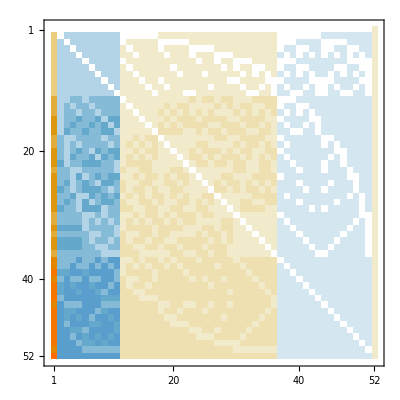

```mathematica
ConversionMatrix["E","C"].ConversionMatrix["C","G"]//MatrixPlot
```

```mathematica
Table[ShowGraph5Least[k]->(allGraphs5[k,"colofourgenerator"]/.RepGraph["G"]),{k,RandomSample[allGraphs5NullAtomKeys,5]}]//TableForm
```

-Graphics-145864→-Graphics-034--Graphics-291608--Graphics-68168--Graphics-7608--Graphics-284625--Graphics-270643--Graphics-263645--Graphics-228543--Graphics-207403--Graphics-98285--Graphics-90765--Graphics-75703--Graphics-30365+-Graphics-295111+2 -Graphics-294151+-Graphics-292511+2 -Graphics-291911+-Graphics-266071+-Graphics-207671+-Graphics-90851+2 -Graphics-75731+-Graphics-30371+2 -Graphics-294881+-Graphics-294400+2 -Graphics-292801+-Graphics-287861+-Graphics-287141+-Graphics-285521+-Graphics-273340+2 -Graphics-273100+2 -Graphics-270941+-Graphics-229621+-Graphics-229360+-Graphics-228820+2 -Graphics-98401+-Graphics-98381+2 -Graphics-98321-4 -Graphics-295230-2 -Graphics-295210-4 -Graphics-295150-4 -Graphics-294970-4 -Graphics-294430-4 -Graphics-292810-2 -Graphics-287950-4 -Graphics-273370-2 -Graphics-229630-4 -Graphics-98410+12 -Graphics-295240
-Graphics-43802→-Graphics-034--Graphics-291608--Graphics-68168--Graphics-22788--Graphics-7608--Graphics-284625--Graphics-263645--Graphics-228543--Graphics-221503--Graphics-207403--Graphics-98285--Graphics-90765--Graphics-30365+-Graphics-295111+2 -Graphics-294151+-Graphics-292511+2 -Graphics-291911+-Graphics-266071+-Graphics-222311+-Graphics-207671+2 -Graphics-90851+-Graphics-75731+2 -Graphics-30371+2 -Graphics-294881+-Graphics-294400+2 -Graphics-292801+-Graphics-287861+2 -Graphics-287141+2 -Graphics-285521+-Graphics-273100+-Graphics-270941+-Graphics-229621+2 -Graphics-229360+2 -Graphics-228820+2 -Graphics-98401+-Graphics-98381+2 -Graphics-98321-4 -Graphics-295230-2 -Graphics-295210-4 -Graphics-295150-5 -Graphics-294970-5 -Graphics-294430-5 -Graphics-292810-4 -Graphics-287950-2 -Graphics-273370-4 -Graphics-229630-5 -Graphics-98410+15 -Graphics-295240
-Graphics-44282→-Graphics-034--Graphics-291608--Graphics-200348--Graphics-22788--Graphics-7608--Graphics-284625--Graphics-263645--Graphics-228543--Graphics-221503--Graphics-98285--Graphics-90765--Graphics-75703--Graphics-30365+2 -Graphics-295111+-Graphics-294151+-Graphics-292511+2 -Graphics-291911+-Graphics-266071+2 -Graphics-222311+-Graphics-207671+-Graphics-90851+-Graphics-75731+2 -Graphics-30371+-Graphics-294881+2 -Graphics-294400+2 -Graphics-292801+2 -Graphics-287861+-Graphics-287141+2 -Graphics-285521+-Graphics-273340+-Graphics-270941+2 -Graphics-229621+-Graphics-229360+2 -Graphics-228820+-Graphics-98401+2 -Graphics-98381+2 -Graphics-98321-4 -Graphics-295230-5 -Graphics-295210-5 -Graphics-295150-2 -Graphics-294970-4 -Graphics-294430-5 -Graphics-292810-4 -Graphics-287950-2 -Graphics-273370-5 -Graphics-229630-4 -Graphics-98410+15 -Graphics-295240
-Graphics-58345→-Graphics-034--Graphics-291608--Graphics-22788--Graphics-7608--Graphics-284625--Graphics-270643--Graphics-228543--Graphics-221503--Graphics-207403--Graphics-98285--Graphics-90765--Graphics-75703--Graphics-30365+-Graphics-295111+-Graphics-294151+2 -Graphics-292511+2 -Graphics-291911+-Graphics-222311+-Graphics-207671+-Graphics-90851+-Graphics-75731+2 -Graphics-30371+2 -Graphics-294881+2 -Graphics-294400+-Graphics-292801+-Graphics-287861+-Graphics-287141+-Graphics-285521+-Graphics-273340+-Graphics-273100+-Graphics-270941+-Graphics-229621+2 -Graphics-229360+2 -Graphics-228820+-Graphics-98401+2 -Graphics-98381+2 -Graphics-98321-2 -Graphics-295230-4 -Graphics-295210-4 -Graphics-295150-4 -Graphics-294970-4 -Graphics-294430-4 -Graphics-292810-2 -Graphics-287950-2 -Graphics-273370-4 -Graphics-229630-4 -Graphics-98410+12 -Graphics-295240
-Graphics-439024→-Graphics-034--Graphics-291608--Graphics-200348--Graphics-22788--Graphics-284625--Graphics-270643--Graphics-263645--Graphics-228543--Graphics-221503--Graphics-207403--Graphics-98285--Graphics-90765--Graphics-30365+2 -Graphics-295111+-Graphics-294151+2 -Graphics-292511+-Graphics-291911+-Graphics-266071+2 -Graphics-222311+-Graphics-207671+-Graphics-90851+-Graphics-30371+2 -Graphics-294881+-Graphics-294400+2 -Graphics-292801+2 -Graphics-287861+-Graphics-287141+2 -Graphics-285521+-Graphics-273340+-Graphics-273100+-Graphics-270941+2 -Graphics-229621+2 -Graphics-229360+-Graphics-228820+-Graphics-98401+-Graphics-98381+-Graphics-98321-4 -Graphics-295230-4 -Graphics-295210-4 -Graphics-295150-4 -Graphics-294970-2 -Graphics-294430-4 -Graphics-292810-4 -Graphics-287950-2 -Graphics-273370-4 -Graphics-229630-2 -Graphics-98410+12 -Graphics-295240

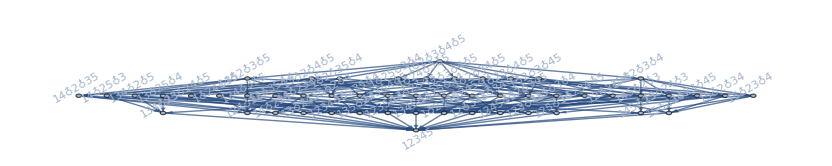
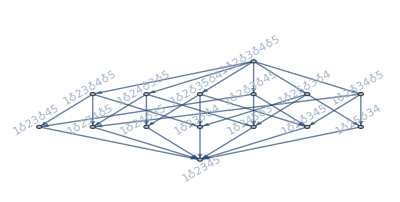
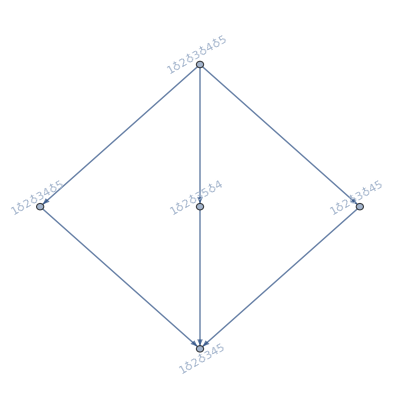
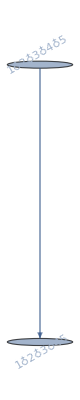
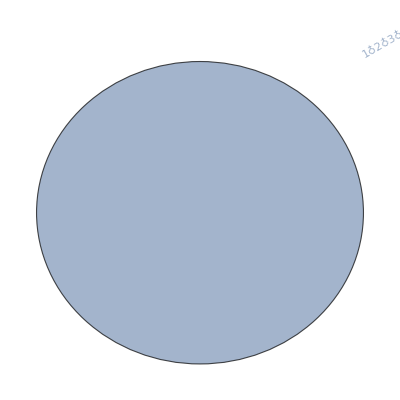
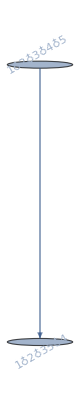
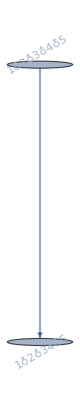
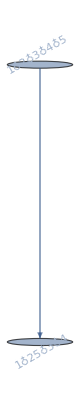
{-Graphics-034→-Graphics-,-Graphics-291608→-Graphics-,-Graphics-295111→-Graphics-,-Graphics-295230→-Graphics-,-Graphics-295240→-Graphics-,-Graphics-295210→-Graphics-,-Graphics-295150→-Graphics-,-Graphics-294970→-Graphics-,-Graphics-294881→-Graphics-,-Graphics-294430→-Graphics-,-Graphics-294400→-Graphics-,-Graphics-294151→-Graphics-,-Graphics-292801→-Graphics-,-Graphics-292810→-Graphics-,-Graphics-292511→-Graphics-,-Graphics-291911→-Graphics-,-Graphics-287950→-Graphics-,-Graphics-287861→-Graphics-,-Graphics-287141→-Graphics-,-Graphics-285521→-Graphics-,-Graphics-284625→-Graphics-,-Graphics-273370→-Graphics-,-Graphics-273340→-Graphics-,-Graphics-273100→-Graphics-,-Graphics-270941→-Graphics-,-Graphics-270643→-Graphics-,-Graphics-266071→-Graphics-,-Graphics-263645→-Graphics-,-Graphics-229621→-Graphics-,-Graphics-229630→-Graphics-,-Graphics-229360→-Graphics-,-Graphics-228820→-Graphics-,-Graphics-228543→-Graphics-,-Graphics-222311→-Graphics-,-Graphics-221503→-Graphics-,-Graphics-207671→-Graphics-,-Graphics-207403→-Graphics-,-Graphics-200348→-Graphics-,-Graphics-98285→-Graphics-,-Graphics-98401→-Graphics-,-Graphics-98410→-Graphics-,-Graphics-98381→-Graphics-,-Graphics-98321→-Graphics-,-Graphics-90851→-Graphics-,-Graphics-90765→-Graphics-,-Graphics-75731→-Graphics-,-Graphics-75703→-Graphics-,-Graphics-68168→-Graphics-,-Graphics-30365→-Graphics-,-Graphics-30371→-Graphics-,-Graphics-22788→-Graphics-,-Graphics-7608→-Graphics-}

```mathematica
Table[ShowGraph5Least[k]->FormulaGraphReverse2[allGraphs5[k,"colofour"]],{k,allGraphs5GeneratorAtomKeys}]
```

```mathematica
Table[ShowGraph5Least[k],{k,allGraphs5FakeAtomKeys}]
```

{-Graphics-034,-Graphics-1968321,-Graphics-295240,-Graphics-287640,-Graphics-272460,-Graphics-264878,-Graphics-264885,-Graphics-227080,-Graphics-219519,-Graphics-219545,-Graphics-204398,-Graphics-204485,-Graphics-1969213,-Graphics-196965,-Graphics-1968615,-Graphics-1968413,-Graphics-656124,-Graphics-94900,-Graphics-87845,-Graphics-87579,-Graphics-73745,-Graphics-72939,-Graphics-664216,-Graphics-66705,-Graphics-658816,-Graphics-656215,-Graphics-218724,-Graphics-31605,-Graphics-29178,-Graphics-243015,-Graphics-24605,-Graphics-221416,-Graphics-219016,-Graphics-72921,-Graphics-97213,-Graphics-10625,-Graphics-81015,-Graphics-73813,-Graphics-24321,-Graphics-3640,-Graphics-3338,-Graphics-2739,-Graphics-24413,-Graphics-8124,-Graphics-1099,-Graphics-8416,-Graphics-2724,-Graphics-3615,-Graphics-921,-Graphics-138,-Graphics-324,-Graphics-121}